```mathematica
h=3
```

3

```mathematica
maxx=50+h
```

53

```mathematica
Clear[f];
f[x_]:=0 /; x<30;
f[x_]:=2*(x-30) /; x<40;
f[x_]:=20+(x-40) /; x≥40;
```

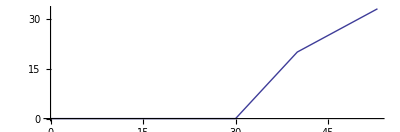

```mathematica
Plot[f[x],{x,0,maxx},PlotRange->All, AspectRatio->35/(2*maxx)]
```

```mathematica
Clear[g];
g[x_]:={-D[f[z],z],1} /. z->x
```

```mathematica
g[1] //N
```

{-0.000362068,1.}

```mathematica
Clear[unitnormal];
unitnormal[x_]:= Normalize[g[x]]
```

```mathematica
Clear[zeroround];
zeroround[{x_,y_}]:={x,0} /; y<0.7;
zeroround[{x_,y_}]:={x,y*(y-0.7)/0.3} /; y<1;
zeroround[{x_,y_}]:={x,y};
```

```mathematica
Clear[thick];
thick[x_]:=h * (1-(x/200));
```

```mathematica
data=Join[Table[
zeroround[{x,f[x]}],{x,0,maxx,1}],
Table[{x,f[x]}+thick[x]*unitnormal[x],{x,maxx,0,-1}]];
data=Join[data, Reverse[data /. {x_,y_}->{-x,y}]];
```

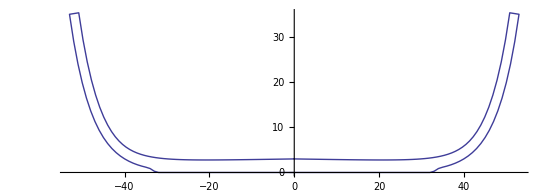

```mathematica
ListPlot[data,PlotJoined->True,PlotRange->All,AspectRatio->35/100]
```

```mathematica
data // N
```

{{0.,0.},{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.},{15.,0.},{16.,0.},{17.,0.},{18.,0.},{19.,0.},{20.,0.},{21.,0.},{22.,0.},{23.,0.},{24.,0.},{25.,0.},{26.,0.},{27.,0.},{28.,0.},{29.,0.},{30.,0.},{31.,0.},{32.,0.},{33.,0.278523},{34.,0.876619},{35.,1.17248},{36.,1.41595},{37.,1.70998},{38.,2.06506},{39.,2.49388},{40.,3.01174},{41.,3.63714},{42.,4.3924},{43.,5.3045},{44.,6.406},{45.,7.73623},{46.,9.34268},{47.,11.2827},{48.,13.6256},{49.,16.455},{50.,19.872},{51.,23.9985},{52.,28.9818},{53.,35.},{50.8199,35.3301},{49.8162,29.3812},{48.8176,24.4804},{47.826,20.4518},{46.8441,17.1494},{45.8751,14.4522},{44.9228,12.2585},{43.9908,10.4825},{43.0819,9.05026},{42.1971,7.89765},{41.3341,6.96903},{40.4877,6.21719},{39.6505,5.60362},{38.8143,5.09837},{37.9718,4.67905},{37.1178,4.32926},{36.2493,4.03687},{35.3651,3.7926},{34.4654,3.58905},{33.5513,3.42012},{32.6243,3.2806},{31.6859,3.16605},{30.7378,3.07263},{29.7812,2.99705},{28.8175,2.93647},{27.8479,2.88849},{26.8733,2.85106},{25.8944,2.82246},{24.912,2.80122},{23.9267,2.78613},{22.939,2.77614},{21.9492,2.77041},{20.9577,2.76821},{19.9648,2.76895},{18.9707,2.77212},{17.9756,2.77732},{16.9797,2.7842},{15.9831,2.79247},{14.9859,2.8019},{13.9883,2.81228},{12.9902,2.82345},{11.9919,2.83528},{10.9932,2.84765},{9.99436,2.86048},{8.99531,2.87368},{7.99609,2.88719},{6.99675,2.90095},{5.99729,2.91493},{4.99775,2.92908},{3.99813,2.94338},{2.99844,2.9578},{1.9987,2.97232},{0.998919,2.98692},{-0.000899433,3.00159},{0.000899433,3.00159},{-0.998919,2.98692},{-1.9987,2.97232},{-2.99844,2.9578},{-3.99813,2.94338},{-4.99775,2.92908},{-5.99729,2.91493},{-6.99675,2.90095},{-7.99609,2.88719},{-8.99531,2.87368},{-9.99436,2.86048},{-10.9932,2.84765},{-11.9919,2.83528},{-12.9902,2.82345},{-13.9883,2.81228},{-14.9859,2.8019},{-15.9831,2.79247},{-16.9797,2.7842},{-17.9756,2.77732},{-18.9707,2.77212},{-19.9648,2.76895},{-20.9577,2.76821},{-21.9492,2.77041},{-22.939,2.77614},{-23.9267,2.78613},{-24.912,2.80122},{-25.8944,2.82246},{-26.8733,2.85106},{-27.8479,2.88849},{-28.8175,2.93647},{-29.7812,2.99705},{-30.7378,3.07263},{-31.6859,3.16605},{-32.6243,3.2806},{-33.5513,3.42012},{-34.4654,3.58905},{-35.3651,3.7926},{-36.2493,4.03687},{-37.1178,4.32926},{-37.9718,4.67905},{-38.8143,5.09837},{-39.6505,5.60362},{-40.4877,6.21719},{-41.3341,6.96903},{-42.1971,7.89765},{-43.0819,9.05026},{-43.9908,10.4825},{-44.9228,12.2585},{-45.8751,14.4522},{-46.8441,17.1494},{-47.826,20.4518},{-48.8176,24.4804},{-49.8162,29.3812},{-50.8199,35.3301},{-53.,35.},{-52.,28.9818},{-51.,23.9985},{-50.,19.872},{-49.,16.455},{-48.,13.6256},{-47.,11.2827},{-46.,9.34268},{-45.,7.73623},{-44.,6.406},{-43.,5.3045},{-42.,4.3924},{-41.,3.63714},{-40.,3.01174},{-39.,2.49388},{-38.,2.06506},{-37.,1.70998},{-36.,1.41595},{-35.,1.17248},{-34.,0.876619},{-33.,0.278523},{-32.,0.},{-31.,0.},{-30.,0.},{-29.,0.},{-28.,0.},{-27.,0.},{-26.,0.},{-25.,0.},{-24.,0.},{-23.,0.},{-22.,0.},{-21.,0.},{-20.,0.},{-19.,0.},{-18.,0.},{-17.,0.},{-16.,0.},{-15.,0.},{-14.,0.},{-13.,0.},{-12.,0.},{-11.,0.},{-10.,0.},{-9.,0.},{-8.,0.},{-7.,0.},{-6.,0.},{-5.,0.},{-4.,0.},{-3.,0.},{-2.,0.},{-1.,0.},{0.,0.}}

```mathematica
Table["v("<>ToString[N[data⟦i⟧⟦1⟧]]<>", "<>ToString[N[data⟦i⟧⟦2⟧]]<>")",{i,1,Length[data]}]
```

{v(0., 0.),v(1., 0.),v(2., 0.),v(3., 0.),v(4., 0.),v(5., 0.),v(6., 0.),v(7., 0.),v(8., 0.),v(9., 0.),v(10., 0.),v(11., 0.),v(12., 0.),v(13., 0.),v(14., 0.),v(15., 0.),v(16., 0.),v(17., 0.),v(18., 0.),v(19., 0.),v(20., 0.),v(21., 0.),v(22., 0.),v(23., 0.),v(24., 0.),v(25., 0.),v(26., 0.),v(27., 0.),v(28., 0.),v(29., 0.),v(30., 0.),v(31., 0.),v(32., 0.),v(33., 0.278523),v(34., 0.876619),v(35., 1.17248),v(36., 1.41595),v(37., 1.70998),v(38., 2.06506),v(39., 2.49388),v(40., 3.01174),v(41., 3.63714),v(42., 4.3924),v(43., 5.3045),v(44., 6.406),v(45., 7.73623),v(46., 9.34268),v(47., 11.2827),v(48., 13.6256),v(49., 16.455),v(50., 19.872),v(51., 23.9985),v(52., 28.9818),v(53., 35.),v(50.8199, 35.3301),v(49.8162, 29.3812),v(48.8176, 24.4804),v(47.826, 20.4518),v(46.8441, 17.1494),v(45.8751, 14.4522),v(44.9228, 12.2585),v(43.9908, 10.4825),v(43.0819, 9.05026),v(42.1971, 7.89765),v(41.3341, 6.96903),v(40.4877, 6.21719),v(39.6505, 5.60362),v(38.8143, 5.09837),v(37.9718, 4.67905),v(37.1178, 4.32926),v(36.2493, 4.03687),v(35.3651, 3.7926),v(34.4654, 3.58905),v(33.5513, 3.42012),v(32.6243, 3.2806),v(31.6859, 3.16605),v(30.7378, 3.07263),v(29.7812, 2.99705),v(28.8175, 2.93647),v(27.8479, 2.88849),v(26.8733, 2.85106),v(25.8944, 2.82246),v(24.912, 2.80122),v(23.9267, 2.78613),v(22.939, 2.77614),v(21.9492, 2.77041),v(20.9577, 2.76821),v(19.9648, 2.76895),v(18.9707, 2.77212),v(17.9756, 2.77732),v(16.9797, 2.7842),v(15.9831, 2.79247),v(14.9859, 2.8019),v(13.9883, 2.81228),v(12.9902, 2.82345),v(11.9919, 2.83528),v(10.9932, 2.84765),v(9.99436, 2.86048),v(8.99531, 2.87368),v(7.99609, 2.88719),v(6.99675, 2.90095),v(5.99729, 2.91493),v(4.99775, 2.92908),v(3.99813, 2.94338),v(2.99844, 2.9578),v(1.9987, 2.97232),v(0.998919, 2.98692),v(-0.000899433, 3.00159),v(0.000899433, 3.00159),v(-0.998919, 2.98692),v(-1.9987, 2.97232),v(-2.99844, 2.9578),v(-3.99813, 2.94338),v(-4.99775, 2.92908),v(-5.99729, 2.91493),v(-6.99675, 2.90095),v(-7.99609, 2.88719),v(-8.99531, 2.87368),v(-9.99436, 2.86048),v(-10.9932, 2.84765),v(-11.9919, 2.83528),v(-12.9902, 2.82345),v(-13.9883, 2.81228),v(-14.9859, 2.8019),v(-15.9831, 2.79247),v(-16.9797, 2.7842),v(-17.9756, 2.77732),v(-18.9707, 2.77212),v(-19.9648, 2.76895),v(-20.9577, 2.76821),v(-21.9492, 2.77041),v(-22.939, 2.77614),v(-23.9267, 2.78613),v(-24.912, 2.80122),v(-25.8944, 2.82246),v(-26.8733, 2.85106),v(-27.8479, 2.88849),v(-28.8175, 2.93647),v(-29.7812, 2.99705),v(-30.7378, 3.07263),v(-31.6859, 3.16605),v(-32.6243, 3.2806),v(-33.5513, 3.42012),v(-34.4654, 3.58905),v(-35.3651, 3.7926),v(-36.2493, 4.03687),v(-37.1178, 4.32926),v(-37.9718, 4.67905),v(-38.8143, 5.09837),v(-39.6505, 5.60362),v(-40.4877, 6.21719),v(-41.3341, 6.96903),v(-42.1971, 7.89765),v(-43.0819, 9.05026),v(-43.9908, 10.4825),v(-44.9228, 12.2585),v(-45.8751, 14.4522),v(-46.8441, 17.1494),v(-47.826, 20.4518),v(-48.8176, 24.4804),v(-49.8162, 29.3812),v(-50.8199, 35.3301),v(-53., 35.),v(-52., 28.9818),v(-51., 23.9985),v(-50., 19.872),v(-49., 16.455),v(-48., 13.6256),v(-47., 11.2827),v(-46., 9.34268),v(-45., 7.73623),v(-44., 6.406),v(-43., 5.3045),v(-42., 4.3924),v(-41., 3.63714),v(-40., 3.01174),v(-39., 2.49388),v(-38., 2.06506),v(-37., 1.70998),v(-36., 1.41595),v(-35., 1.17248),v(-34., 0.876619),v(-33., 0.278523),v(-32., 0.),v(-31., 0.),v(-30., 0.),v(-29., 0.),v(-28., 0.),v(-27., 0.),v(-26., 0.),v(-25., 0.),v(-24., 0.),v(-23., 0.),v(-22., 0.),v(-21., 0.),v(-20., 0.),v(-19., 0.),v(-18., 0.),v(-17., 0.),v(-16., 0.),v(-15., 0.),v(-14., 0.),v(-13., 0.),v(-12., 0.),v(-11., 0.),v(-10., 0.),v(-9., 0.),v(-8., 0.),v(-7., 0.),v(-6., 0.),v(-5., 0.),v(-4., 0.),v(-3., 0.),v(-2., 0.),v(-1., 0.),v(0., 0.)}